# Relaxation

Malcolm Levitt & Christian Bengs 20-Feb-2025
This documentation applies to SpinDynamica v3.10

Parts 1-5 of this documentation should be read first.

## Setup

The code in this notebook requires the installation and initialization of SpinDynamica, as described in part 1 of the documentation

```mathematica
Needs["SpinDynamica`"];
SetSpinSystem[1];
```

SpinDynamica version SDv3.9.1b3 loaded by Mathematica 14.1 running on Mac OS X ARM (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Dot,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

SpinDynamica::badinfo: In some cases, requesting information by executing "?<symbol>") generates an infinite loop. I have not been able to identify why this happens. In these cases, readable information on a symbol may be generated by executing "<symbol>::usage". Apologies from MHL.

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

Relaxation may be included in SpinDynamica by including an appropriate superoperator as the evolution generator. This may be done either phenomenologically (which means just including a term which corresponds to the experimental results), or by including the  superoperator corresponding to a particular relaxation mechanism, or set of mechanisms.

## Phenomenological Relaxation

### PhenomenologicalRelaxationSuperoperator

A Phenomenological Relaxation Superoperators employing a longitudinal relaxation time constant T_1 and a transverse relaxation time constant T_2 may be constructed using PhenomenologicalRelaxationSuperoperator. 

The general syntax is PhenomenologicalRelaxationSuperoperator[{{lab#1,T1#1,T2#1},{lab#2,T1#2,T2#2},...}] where lab#j refers to the label of spin j and T1#j / T2#j refer to the T_1 and T_2 time constants of spin j.

Consider, for example, an ensemble of single spins-1/2, with T_1=2.0 s and T_2=0.9 s. The appropriate relaxation superoperator may be generated as shown below:

```mathematica
SetSpinSystem[1];Γ=PhenomenologicalRelaxationSuperoperator[{{1,2.0,0.9}}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

Superoperator[<<..>>, SuperoperatorType→"Hermitian"]

The basis operators of the Cartesian product operator basis for this system are as follows:

```mathematica
BasisOperators[CartesianProductOperatorBasis[]]
```

{𝟙/(√2),√2 I_(1x),√2 I_(1y),√2 I_(1z)}

The SuperoperatorMatrixRepresentation of the Relaxation Superoperator in this basis takes the following form:

```mathematica
SuperoperatorMatrixRepresentation[Γ,CartesianProductOperatorBasis[]]//MatrixForm//Chop
```

(0 | 0 | 0 | 0
0 | -1.11111 | 0 | 0
0 | 0 | -1.11111 | 0
0 | 0 | 0 | -0.5)

Note that an eigenvalue of 0 is found for the unity operator. This corresponds to the physical constraint that the sum of all populations is constant (assuming a closed system).

The evolution of transverse magnetization under this relaxation superoperator is easily calculated using Trajectory:

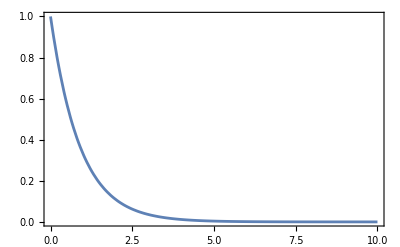

```mathematica
trajx=Trajectory[opI["x"]->opI["x"],{None,10},BackgroundGenerator->Γ];
Plot[trajx[t],{t,0,10},PlotRange->All]
```

A resonance offset term may be included by combining a spin Hamiltonian and a relaxation superoperator using CombineGenerators:

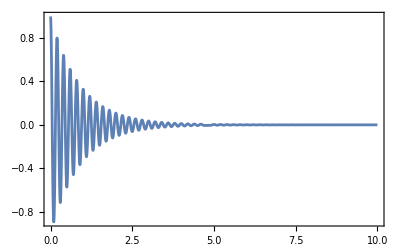

```mathematica
Hoff=2π 5 opI["z"];
trajx=Trajectory[opI["x"]->opI["x"],{None,10},BackgroundGenerator->CombineGenerators[Hoff,Γ]];
Plot[trajx[t],{t,0,10},PlotRange->All]
```

The evolution of the z-magnetization may be calculated in a similar way:

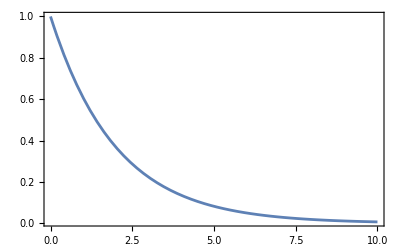

```mathematica
Hoff=2π 5 opI["z"];
trajz=Trajectory[opI["z"]->opI["z"],{None,10},BackgroundGenerator->CombineGenerators[Hoff,Γ]];
Plot[trajz[t],{t,0,10},PlotRange->All]
```

Note that the relaxation of the longitudinal magnetization is towards 0, i.e. a state of infinite temperature. This happens because the finite temperature of the sample has not yet been taken into account.

### thermal equilibrium and thermalization

The thermal equilibrium density operator at a given temperature, in the presence of an arbitrary laboratory frame Hamiltonian, may be calculated using ThermalEquilibriumDensityOperator. For example, suppose that the magnetic field is 11.7 T, the sample temperature is 300 Kelvin, and the spin-1/2 species are protons. The thermal equilibrium density operator is calculated as follows:

```mathematica
SetSpinSystem[1];
ω0lab=LarmorFrequency[1,11.7];
Hlab=ω0lab opI["z"];
ρeq=ThermalEquilibriumDensityOperator[Hlab,300]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

Operator[<<..>>, OperatorType→Hermitian ]

The matrix representation of the thermal equilibrium density operator may be calculated in the usual way:

```mathematica
MatrixRepresentation[ρeq]//MatrixForm
```

(0.50002 | 0
0 | 0.49998)

Note the small excess of population in the |α> state relative to the |β> state. The thermal equilibrium coefficient of I_z may be deduced by using OperatorAmplitude:

```mathematica
Meq=OperatorAmplitude[ρeq->opI["z"]]
Meq//EngineeringForm
```

0.0000398462

39.8462×10^-6

Relaxation towards thermal equilibrium at the finite sample temperature is imposed by applying ThermalizeSuperoperator to the relaxation superoperator:

```mathematica
Γtherm=ThermalizeSuperoperator[Γ,Hlab,300]
```

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

Superoperator[<<..>>, SuperoperatorType→None]

Note, however, that the ThermalizeSuperoperator procedure is not rigorous for spin systems that are far from equilibrium or contain large amounts of spin order. The correct method is to use Lindbladian superoperators, as described in Bengs and Levitt, doi.org/10.1016/j.jmr.2019.106645. The SpinDynamica implementation of Lindbladians is given in an example below.

An inversion-recovery experiment, starting from thermal equilibrium, and monitoring the z-magnetization, may be simulated as follows:

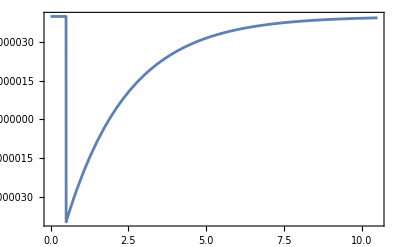

```mathematica
Hoff=2π 5 opI["z"];
trajz=Trajectory[ρeq->opI["z"],{{None,1/2},RotationSuperoperator[{π,"x"}],{None,10}},BackgroundGenerator->CombineGenerators[Hoff,Γtherm]];
Plot[trajz[t],{t,0,10.5},PlotRange->All]
```

The result is conveniently scaled to the thermal equilibrium magnetization, by using NormalizationFactor:

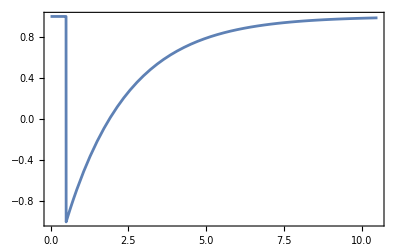

```mathematica
Hoff=2π 5 opI["z"];
trajz=Trajectory[ρeq->opI["z"],{{None,1/2},RotationSuperoperator[{π,"x"}],{None,10}},BackgroundGenerator->CombineGenerators[Hoff,Γtherm],
NormalizationFactor->Meq
];
Plot[trajz[t],{t,0,10.5},PlotRange->All]
```

Magnetization trajectories after a 90° pulse may be simulated in the presence of relaxation:

```mathematica
Hoff=2π 5 opI["z"];
{trajx,trajy,trajz}=Trajectory[
ρeq->{opI["x"],opI["y"],opI["z"]},
{RotationSuperoperator[{π/2,"x"}],{None,10}},BackgroundGenerator->CombineGenerators[Hoff,Γtherm],
NormalizationFactor->Meq
];
Show[
SphereAndAxes[],
ParametricPlot3D[
{trajx[t],trajy[t],trajz[t]},{t,0,10},
Axes->None,PlotStyle->{{Thick,Blue}}
],
Boxed->False
]
```

-Graphics3D-

Magnetization trajectories may be simulated in the presence of any sequence of events by including the thermalized relaxation superoperator in the BackgroundGenerator. For example, the simulation below involves a strong 90° pulse about the x-axis followed by a weak rf field along the y-axis, which is partially successful in spin-locking the magnetization.

```mathematica
Hoff=2π 5 opI["z"];
{trajx,trajy,trajz}=Trajectory[
ρeq->{opI["x"],opI["y"],opI["z"]},
{RotationSuperoperator[{π/2,"x"}],{2π 20 opI["y"],10}},BackgroundGenerator->CombineGenerators[Hoff,Γtherm],
NormalizationFactor->Meq
];
Show[
SphereAndAxes[],
ParametricPlot3D[
{trajx[t],trajy[t],trajz[t]},{t,0,10},
Axes->None,PlotStyle->{{Thick,Blue}},
PlotPoints->200
],
Boxed->False
]
```

-Graphics3D-

### personalized Phenomenological Relaxation Superoperator

SpinDynamica allows the definition of personalized Phenomenological Relaxation Superoperators. The PhenomonologicalRelaxationSuperoperator may involve any relaxation rate constants for the relevant spin operators, and also any cross-relaxation rate constants between the relevant operators. However, care is needed to ensure that the simulated relaxation matrix is physically plausible.

For example, in the case of a 2-spin-1/2 system, there are 16 Cartesian product operators:

```mathematica
SetSpinSystem[2];
BasisOperators[CartesianProductOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

{𝟙/2,I_(1x),I_(1y),I_(1z),I_(2x),I_(2y),I_(2z),2 (I_(1x)•I_(2x)),2 (I_(1x)•I_(2y)),2 (I_(1x)•I_(2z)),2 (I_(1y)•I_(2x)),2 (I_(1y)•I_(2y)),2 (I_(1y)•I_(2z)),2 (I_(1z)•I_(2x)),2 (I_(1z)•I_(2y)),2 (I_(1z)•I_(2z))}

The following set of rate constants corresponds to 2 s relaxation times for all the z-operators, and 1 second relaxation times for all the x and y operators:

```mathematica
Tlong=2;
Ttrans=1;
RateConstants=Join[{0},{1/Ttrans,1/Ttrans,1/Tlong},{1/Ttrans,1/Ttrans,1/Tlong},Table[1/Ttrans,{8}],{1/Tlong}]
Length[%]
```

{0,1,1,1/2,1,1,1/2,1,1,1,1,1,1,1,1,1/2}

16

The appropriate relaxation superoperator is defined as follows:

```mathematica
Γ=Superoperator[DiagonalMatrix[-RateConstants],CartesianProductOperatorBasis[]]
Γ//SuperoperatorMatrixRepresentation//MatrixForm
```

Superoperator[<<..>>, SuperoperatorType→"Hermitian"]

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

The evolution of transverse magnetization under this relaxation superoperator is easily calculated using Trajectory:

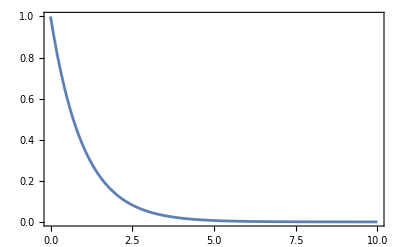

```mathematica
trajx=Trajectory[opI["x"]->opI["x"],{None,10},BackgroundGenerator->Γ];
Plot[trajx[t],{t,0,10},PlotRange->All]
```

The other calculations follow as before.

Cross-relaxation and cross-correlated relaxation terms are readily included as off-diagonal elements in the matrix argument of Superoperator. However, a relaxation superoperator defined this way does not necessarily correspond to a plausible physical mechanism.

## Relaxation Models

Realistic relaxation models are simulated in SpinDynamica by specifying the relaxation superoperator which describes a particular mechanism within Abragam-Redfield relaxation theory.  Texts such as J. Kowalewski and L. Mäler, “Nuclear Spin Relaxation in Liquids: Theory, Experiments and Applications.” (CRC Press, Boca Raton, Florida, 2006) may be consulted to discover the appropriate form of the relaxation superoperator in specific cases. In most cases the relaxation superoperator involves a combination of DoubleCommutationSuperoperator objects. SpinDynamica is capable of handling very general forms, including arbitrary correlation times, motional models, cross-correlation effects, and so on. Only a few simple models are given here.

### Random field relaxation (extreme narrowing)

Random field relaxation may be simulated by using a DoubleCommutationSuperoperator between Cartesian angular momentum operator components. For example, if the random field has magnitude ωrms (in frequency units), and correlation time τc, then the appropriate relaxation superoperator for an isotropic random field, in the extreme narrowing limit, is as follows:

```mathematica
SetSpinSystem[1];
Γran=-(1/2)ωrms^2 τc (DoubleCommutationSuperoperator[opI["x"],opI["x"]]+DoubleCommutationSuperoperator[opI["y"],opI["y"]]+DoubleCommutationSuperoperator[opI["z"],opI["z"]]);
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

This superoperator is diagonal in the Cartesian product operator basis:

```mathematica
SuperoperatorMatrixRepresentation[Γran,CartesianProductOperatorBasis[]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | -τc ωrms^2 | 0 | 0
0 | 0 | -τc ωrms^2 | 0
0 | 0 | 0 | -τc ωrms^2)

From this one may see that T_1 and T_2 are equal in this model, and are both given by 1/(ωrms^2 τc).

### Random field relaxation (slow motion limit)

In the limit of slow random field fluctuations, only the z-components are included in the relaxation superoperator:

```mathematica
SetSpinSystem[1];
Γran=-(1/2)ωrms^2 τc DoubleCommutationSuperoperator[opI["z"],opI["z"]];
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

```mathematica
SuperoperatorMatrixRepresentation[Γran,CartesianProductOperatorBasis[]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | -(τc ωrms^2)/2 | 0 | 0
0 | 0 | -(τc ωrms^2)/2 | 0
0 | 0 | 0 | 0)

A slow-motion relaxation superoperator of this type leads to transverse relaxation, but not longitudinal relaxation.

### Dipole-dipole relaxation (extreme narrowing): homonuclear case

Dipole-dipole relaxation may be simulated by summing DoubleCommutationSuperoperator terms involving the second-rank spherical tensor operators for the involved spins. For example, for 2 spins-1/2 with a DD coupling ωDD, in the extreme narrowing limit, the appropriate superoperator is as follows:

```mathematica
SetSpinSystem[2];
ΓDD=-(6/5)ωDD^2 τc Sum[(-1)^m DoubleCommutationSuperoperator[opT[{1,2},{2,m}],opT[{1,2},{2,-m}]],{m,-2,2}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

-6/5 τc ωDD^2 (DoubleCommutationSuperoperator[1/2 (I_1^-•I_2^-),1/2 (I_1^+•I_2^+)]+DoubleCommutationSuperoperator[1/2 (I_1^+•I_2^+),1/2 (I_1^-•I_2^-)]-DoubleCommutationSuperoperator[1/2 (I_1^-•I_(2z)+I_(1z)•I_2^-),1/2 (-(I_1^+•I_(2z))-I_(1z)•I_2^+)]-DoubleCommutationSuperoperator[1/2 (-(I_1^+•I_(2z))-I_(1z)•I_2^+),1/2 (I_1^-•I_(2z)+I_(1z)•I_2^-)]+DoubleCommutationSuperoperator[-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6),-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6)])

This has the following matrix representation in the Cartesian product operator basis:

```mathematica
SuperoperatorMatrixRepresentation[ΓDD,CartesianProductOperatorBasis[]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -τc ωDD^2 | 0 | 0 | -(τc ωDD^2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -τc ωDD^2 | 0 | 0 | -(τc ωDD^2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -τc ωDD^2 | 0 | 0 | -(τc ωDD^2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(τc ωDD^2)/2 | 0 | 0 | -τc ωDD^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(τc ωDD^2)/2 | 0 | 0 | -τc ωDD^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(τc ωDD^2)/2 | 0 | 0 | -τc ωDD^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 τc ωDD^2)/5 | 0 | 0 | 0 | (3 τc ωDD^2)/10 | 0 | 0 | 0 | (3 τc ωDD^2)/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(7 τc ωDD^2)/10 | 0 | -(τc ωDD^2)/5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(7 τc ωDD^2)/10 | 0 | 0 | 0 | -(τc ωDD^2)/5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(τc ωDD^2)/5 | 0 | -(7 τc ωDD^2)/10 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 τc ωDD^2)/10 | 0 | 0 | 0 | -(3 τc ωDD^2)/5 | 0 | 0 | 0 | (3 τc ωDD^2)/10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(7 τc ωDD^2)/10 | 0 | -(τc ωDD^2)/5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(τc ωDD^2)/5 | 0 | 0 | 0 | -(7 τc ωDD^2)/10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(τc ωDD^2)/5 | 0 | -(7 τc ωDD^2)/10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 τc ωDD^2)/10 | 0 | 0 | 0 | (3 τc ωDD^2)/10 | 0 | 0 | 0 | -(3 τc ωDD^2)/5)

This superoperator may be used to simulate what happens in a 2-spin-1/2 system if the longitudinal magnetization is inverted on just one of the 2 spins, and then the spin system is allowed to evolve. For example, suppose that the DD coupling is 20 kHz, and the correlation time is 10 ps. The trajectories of the longitudinal magnetization components are as follows:

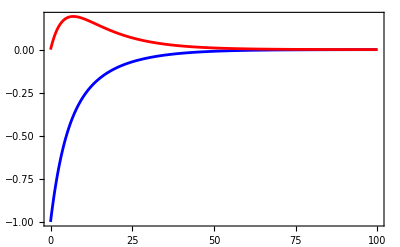

```mathematica
{traj1z,traj2z}=Trajectory[
-opI[1,"z"]->{opI[1,"z"],opI[2,"z"]},
{None,100},
BackgroundGenerator->(ΓDD/.{ωDD->2π 20 10^3,τc->10 10^-12})
];
Plot[{traj1z[t],traj2z[t]},{t,0,100},PlotRange->All,PlotStyle->{Blue,Red}]
```

Note the transient enhancement of the magnetization on the non-inverted spin. This is a manifestation of the nuclear Overhauser effect.

### Dipole-dipole relaxation (extreme narrowing): heteronuclear case

When heteronuclear spin systems are involved, it is necessary to secularize the relaxation superoperator against the Zeeman Hamiltonian before use. This is conveniently done using the Secularize routine of SpinDynamica.

First set up the dipolar relaxation superoperator, as for the homonuclear system:

```mathematica
SetSpinSystem[2];
ΓDD=-(6/5)ωDD^2 τc Sum[(-1)^m DoubleCommutationSuperoperator[opT[{1,2},{2,m}],opT[{1,2},{2,-m}]],{m,-2,2}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

-6/5 τc ωDD^2 (DoubleCommutationSuperoperator[1/2 (I_1^-•I_2^-),1/2 (I_1^+•I_2^+)]+DoubleCommutationSuperoperator[1/2 (I_1^+•I_2^+),1/2 (I_1^-•I_2^-)]-DoubleCommutationSuperoperator[1/2 (I_1^-•I_(2z)+I_(1z)•I_2^-),1/2 (-(I_1^+•I_(2z))-I_(1z)•I_2^+)]-DoubleCommutationSuperoperator[1/2 (-(I_1^+•I_(2z))-I_(1z)•I_2^+),1/2 (I_1^-•I_(2z)+I_(1z)•I_2^-)]+DoubleCommutationSuperoperator[-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6),-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6)])

Now secularize it, assuming that spins #1 and #2 belong to different isotopic types:

```mathematica
Ispins={1};
Sspins={2};
ΓDDsec=Secularize[ΓDD,{Ispins,Sspins}]
```

Superoperator[<<..>>, SuperoperatorType→Undefined]

The secularized superoperator has fewer elements:

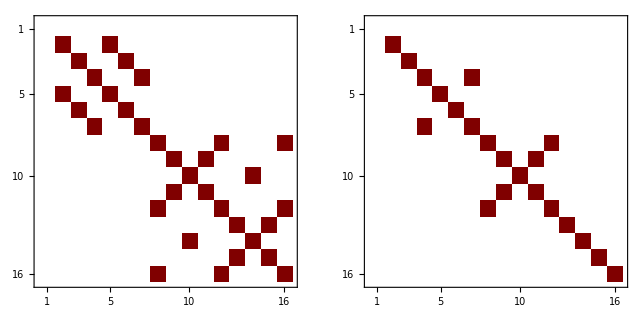

```mathematica
GraphicsRow[{MatrixPlot[SuperoperatorMatrixRepresentation[ΓDD,CartesianProductOperatorBasis[]]],MatrixPlot[SuperoperatorMatrixRepresentation[ΓDDsec,CartesianProductOperatorBasis[]]]}]
```

This secularized superoperator may be used to calculate the transient NOE:

```mathematica
{traj1z,traj2z}=Trajectory[
-opI[1,"z"]->{opI[1,"z"],opI[2,"z"]},
{None,100},
BackgroundGenerator->(ΓDDsec/.{ωDD->2π 20 10^3,τc->10 10^-12})
];
Plot[{traj1z[t],traj2z[t]},{t,0,100},PlotRange->All,PlotStyle->{Blue,Red}]
```

Trajectory::suspsymbs: The following symbols do not have numerical values: {τc,ωDD}.

Set::shape: Lists {traj1z,traj2z} and $Failed are not the same shape.

-Graphics-

In this particular case the results of the secularized and non-secularized calculations are identical. However this is not always the case.

### Dipole-dipole relaxation (slow motion limit): homonuclear case

In the slow-motion limit, only the m=0 components of the relaxation superoperator are involved:

```mathematica
SetSpinSystem[2];
ΓDD=-(6/5)ωDD^2 τc × DoubleCommutationSuperoperator[opT[{1,2},{2,0}],opT[{1,2},{2,0}]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

-6/5 τc ωDD^2 DoubleCommutationSuperoperator[-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6),-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6)]

For example, suppose that the DD coupling is 20 kHz, and the correlation time is 10 ns. The trajectories of the longitudinal magnetization components are now as follows:

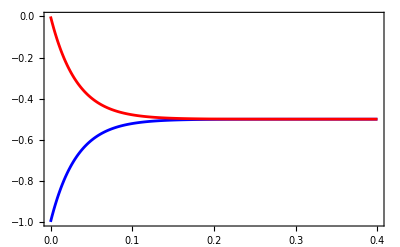

```mathematica
{traj1z,traj2z}=Trajectory[
-opI[1,"z"]->{opI[1,"z"],opI[2,"z"]},
{None,0.4},
BackgroundGenerator->(ΓDD/.{ωDD->2π 20 10^3,τc->10 10^-9})
];
Plot[{traj1z[t],traj2z[t]},{t,0,0.4},PlotRange->All,PlotStyle->{Blue,Red}]
```

Note that the magnetization components now converge, as they equilibrate through cross-relaxation.

The general relaxation superoperator for DD relaxation involves all of the terms used in the extreme narrowing case, but weighted by spectral densities. Consult the literature for the correct form.

### Dipole-dipole relaxation (with thermalization using ThermalizeSuperoperator)

The examples above are appropriate for an infinite sample temperature. For a finite temperature, the relaxation superoperator must be thermalized. This may be done either by using ThermalizeSuperoperator or by using Lindbladian superoperators.

Consider a extreme-narrowing-limit relaxation superoperator:

```mathematica
SetSpinSystem[2];
ΓDD=-(6/5)ωDD^2 τc Sum[(-1)^m DoubleCommutationSuperoperator[opT[{1,2},{2,m}],opT[{1,2},{2,-m}]],{m,-2,2}];
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Suppose that the DD coupling is 20 kHz, and the correlation time is 10 ps. If the laboratory frame Hamiltonian is appropriate for protons in a magnetic field of 11.7 T, and the sample temperature is 300 Kelvin, the thermalized relaxation superoperator is as follows:

```mathematica
H0=LarmorFrequency[1,11.7]opI["z"];
ΓDDtherm=ThermalizeSuperoperator[ΓDD/.{ωDD->2π 20 10^3,τc->10 10^-12},H0,300]
```

Superoperator[<<..>>, SuperoperatorType→None]

As described above, this thermalization procedure is not rigorous for spin systems that are far from equilibrium or contain a large amount of spin order. The more rigorous Lindbladian procedure is demonstrated below.

The thermal equilibrium density operator under the same conditions is as follows:

```mathematica
ρeq=ThermalEquilibriumDensityOperator[H0,300]
```

Operator[<<..>>, OperatorType→Hermitian ]

The thermal equilibrium magnetization may be defined:

```mathematica
Meq=OperatorAmplitude[ρeq->opI[1,"z"]];
```

The trajectory of the two z-magnetizations, after inversion of one set of spins, is as follows:

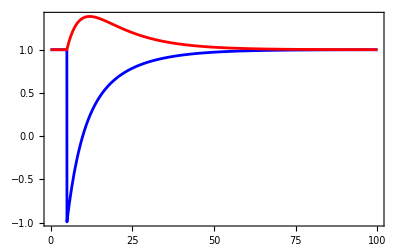

```mathematica
{traj1z,traj2z}=Trajectory[
ρeq->{opI[1,"z"],opI[2,"z"]},
{{None,5},RotationSuperoperator[1,{π,"x"}],{None,100}},
BackgroundGenerator->ΓDDtherm,
NormalizationFactor->Meq
];
Plot[{traj1z[t],traj2z[t]},{t,0,100},PlotRange->All,PlotStyle->{Blue,Red}]
```

Note that the two magnetization components now recover back to their thermal equilibrium values, with a transient NOE developing on the non-inverted set of spins, immediately after the inversion.

### Dipole-dipole relaxation (with Lindblad thermalization)

The case of dipole-dipole relaxation may also be thermalized using Lindbladian superoperators. As discussed in Bengs and Levitt, doi.org/10.1016/j.jmr.2019.106645, this is more rigorous than the ThermalizeSuperoperator method, especially in the case of large amounts of spin order or far-from-equilibrium spin systems.

Consider an ensemble of proton pairs, in a magnetic field of 11.7 T and a sample temperature of 300 Kelvin. The dipole-dipole coupling is -20 kHz, and the rotational correlation time 10 ps.

```mathematica
parameters={B0->11.7, T->300,ωDD->2π 20 10^3,τc->10 10^-12};
```

The Lindbladian form of the thermalized relaxation superoperator, in the extreme narrowing limit, is set up as follows:

```mathematica
SetSpinSystem[2];
ΓDDLB=+(6/5)ωDD^2(2τc) Sum[(-1)^m Lindbladian[opT[{1,2},{2,m}],opT[{1,2},{2,-m}]]Exp[-(1/2)m ℏ ω0/(kB T)],{m,-2,2}]/.{ω0->LarmorFrequency[1,B0]}/.parameters/.PhysicalConstantValues//N
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

0.378993 (0.99992 Lindbladian[0.5 (I_1^-•I_2^-),0.5 (I_1^+•I_2^+)]+1.00008 Lindbladian[0.5 (I_1^+•I_2^+),0.5 (I_1^-•I_2^-)]-0.99996 Lindbladian[0.5 (I_1^-•I_(2z)+I_(1z)•I_2^-),0.5 (-1. (I_1^+•I_(2z))-1. (I_(1z)•I_2^+))]-1.00004 Lindbladian[0.5 (-1. (I_1^+•I_(2z))-1. (I_(1z)•I_2^+)),0.5 (I_1^-•I_(2z)+I_(1z)•I_2^-)]+Lindbladian[-0.204124 (I_1^-•I_2^++I_1^+•I_2^--4. (I_(1z)•I_(2z))),-0.204124 (I_1^-•I_2^++I_1^+•I_2^--4. (I_(1z)•I_(2z)))])

Note the positive sign and the factor (2τc) in the expression for the Lindbladian relaxation superoperator. These factors derive from eqs. 151 and 153 of the Bengs & Levitt paper (doi.org/10.1016/j.jmr.2019.106645).

The thermal equilibrium density operator under the same conditions is as follows:

```mathematica
H0=ω0 opI["z"]/.{ω0->LarmorFrequency[1,B0]}/.parameters
ρeq=ThermalEquilibriumDensityOperator[H0,300]
```

-3.13001×10^9 (I_(1z)+I_(2z))

Operator[<<..>>, OperatorType→Hermitian ]

The thermal equilibrium magnetization is defined:

```mathematica
Meq=OperatorAmplitude[ρeq->opI[1,"z"]];
```

The trajectory of the two z-magnetizations, after inversion of one set of spins, is as follows:

```mathematica
{traj1z,traj2z}=Trajectory[
ρeq->{opI[1,"z"],opI[2,"z"]},
{{None,5},Pulse[1,{π,"x"}],{None,100}},
BackgroundGenerator->ΓDDLB,
NormalizationFactor->Meq
];
Plot[{traj1z[t],traj2z[t]},{t,0,100},PlotRange->All,PlotStyle->{Blue,Red}]
```

-Graphics-

In this case, the Lindbladian relaxation superoperator gives the same result as the thermalized DoubleCommutationSuperoperator (see above).

## Relaxation Phenomena

### Cross-relaxation and transient NOE

See the examples above for cross-relaxation trajectories and transient NOE effects, with and without thermalization

### Long-lived singlet order

Homonuclear dipole-dipole relaxation generates T1 relaxation, but not decay of singlet order. The example below employs Lindblad thermalization in the extreme narrowing limit.

```mathematica
SetSpinSystem[2];
parameters={B0->11.7, T->300,ωDD->2π 20 10^3,τc->10 10^-12};
ΓDDLB=+(6/5)ωDD^2(2τc) Sum[(-1)^m Lindbladian[opT[{1,2},{2,m}],opT[{1,2},{2,-m}]]Exp[-(1/2)m ℏ ω0/(kB T)],{m,-2,2}]/.{ω0->LarmorFrequency[1,B0]}/.parameters/.PhysicalConstantValues
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

24/625 π^2 (0.99992 Lindbladian[1/2 (I_1^-•I_2^-),1/2 (I_1^+•I_2^+)]+1.00008 Lindbladian[1/2 (I_1^+•I_2^+),1/2 (I_1^-•I_2^-)]-0.99996 Lindbladian[1/2 (I_1^-•I_(2z)+I_(1z)•I_2^-),1/2 (-(I_1^+•I_(2z))-I_(1z)•I_2^+)]-1.00004 Lindbladian[1/2 (-(I_1^+•I_(2z))-I_(1z)•I_2^+),1/2 (I_1^-•I_(2z)+I_(1z)•I_2^-)]+Lindbladian[-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6),-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(2 √6)])

The thermal equilibrium density operator is set up:

```mathematica
H0=ω0 opI["z"]/.{ω0->LarmorFrequency[1,B0]}/.parameters;
ρeq=ThermalEquilibriumDensityOperator[H0,300];
Meq=OperatorAmplitude[ρeq->opI[1,"z"]];
```

The trajectories below exhibit transient cross-relaxation effects after inverting the magnetization of one of the spin species.

```mathematica
{traj1z,traj2z}=Trajectory[
ρeq->{opI[1,"z"],opI[2,"z"]},
{{None,5},Pulse[1,{π,"x"}],{None,100}},
BackgroundGenerator->ΓDDLB,
NormalizationFactor->Meq
];
Plot[{traj1z[t],traj2z[t]},{t,0,100},PlotRange->All,PlotStyle->{Blue,Red}]
```

-Graphics-

Singlet order, on the other hand, does not decay

```mathematica
SO=opI[1].opI[2]
```

(I⃗)_1•(I⃗)_2

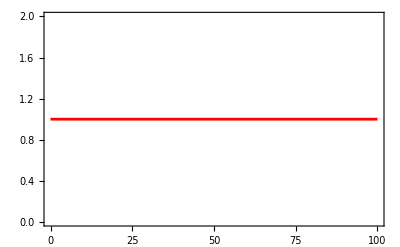

```mathematica
trajS=Trajectory[
Meq SO->SO,
{None,100},
BackgroundGenerator->ΓDDLB,
NormalizationFactor->Meq
];
Plot[trajS[t],{t,0,100},PlotRange->All,PlotStyle->{Blue,Red}]
```